```mathematica
DEigensystem[{-ψ''[x]/(2m),DirichletCondition[ψ[x]==0,True]},ψ[x],{x,0,1},4]
```

{{π^2/(2 m),(2 π^2)/m,(9 π^2)/(2 m),(8 π^2)/m},{Sin[π x],Sin[2 π x],Sin[3 π x],Sin[4 π x]}}

```mathematica
DEigensystem[{1/2(-ψ''[ϕ]+Ω^2 ψ[ϕ]),DirichletCondition[ψ[ϕ]==0,True]},ψ[ϕ],{ϕ,-∞,+∞},4]
```

DEigensystem[{1/2 (Ω^2 ψ[ϕ]-ψ''[ϕ]),DirichletCondition[ψ[ϕ]==0,True]},ψ[ϕ],{ϕ,-∞,∞},4]

```mathematica
am[ψ_,ϕ_]:=1/(√2)(Ω^(+1/2)ϕ ψ+Ω^(-1/2)D[ψ,ϕ])
ap[ψ_,ϕ_]:=1/(√2)(Ω^(+1/2)ϕ ψ-Ω^(-1/2)D[ψ,ϕ])
deq=FullSimplify@am[ψ[ϕ],ϕ]==0
(*ap[am[ϕ↦ψ[ϕ],ϕ][ϕ],ϕ][ϕ]*)
sol=DSolve[deq,ψ[ϕ],ϕ]
ap[ψ[ϕ]/.sol[[1]],ϕ]//Simplify
ap[%,ϕ]//Simplify
FullSimplify[FoldList[ap,ψ[ϕ]/.sol[[1]],Table[ϕ,7]]/Table[√(n!),{n,0,7}]]
Table[1/(√(2^n n!))ⅇ^(-Ω/2 ϕ^2)HermiteH[n,√Ω ϕ],{n,0,7}]//FullSimplify
%%/%
(*%/(ψ[ϕ]/.sol[[1]])/.{ϕ->x/(√Ω)}//FullSimplify
%Table[√(2^n n!),{n,0,10}]*)
ClearAll[deq]
ClearAll[am,ap]
ClearAll[sol]d
```

(ϕ Ω ψ[ϕ]+ψ'[ϕ])/(√2 √Ω)==0

{{ψ[ϕ]→ⅇ^(-(ϕ^2 Ω)/2) C[1]}}

√2 ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω C[1]

ⅇ^(-(ϕ^2 Ω)/2) (-1+2 ϕ^2 Ω) C[1]

{ⅇ^(-(ϕ^2 Ω)/2) C[1],√2 ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω C[1],(ⅇ^(-(ϕ^2 Ω)/2) (-1+2 ϕ^2 Ω) C[1])/(√2),(ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω (-3+2 ϕ^2 Ω) C[1])/(√3),(ⅇ^(-(ϕ^2 Ω)/2) (3+4 ϕ^2 Ω (-3+ϕ^2 Ω)) C[1])/(2 √6),(ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω (15+4 ϕ^2 Ω (-5+ϕ^2 Ω)) C[1])/(2 √15),(ⅇ^(-(ϕ^2 Ω)/2) (-15+90 ϕ^2 Ω-60 ϕ^4 Ω^2+8 ϕ^6 Ω^3) C[1])/(12 √5),(ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω (-105+210 ϕ^2 Ω-84 ϕ^4 Ω^2+8 ϕ^6 Ω^3) C[1])/(6 √70)}

{ⅇ^(-(ϕ^2 Ω)/2),√2 ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω,(ⅇ^(-(ϕ^2 Ω)/2) (-1+2 ϕ^2 Ω))/(√2),(ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω (-3+2 ϕ^2 Ω))/(√3),(ⅇ^(-(ϕ^2 Ω)/2) (3+4 ϕ^2 Ω (-3+ϕ^2 Ω)))/(2 √6),(ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω (15+4 ϕ^2 Ω (-5+ϕ^2 Ω)))/(2 √15),(ⅇ^(-(ϕ^2 Ω)/2) (-15+90 ϕ^2 Ω-60 ϕ^4 Ω^2+8 ϕ^6 Ω^3))/(12 √5),(ⅇ^(-(ϕ^2 Ω)/2) ϕ √Ω (-105+210 ϕ^2 Ω-84 ϕ^4 Ω^2+8 ϕ^6 Ω^3))/(6 √70)}

{C[1],C[1],C[1],C[1],C[1],C[1],C[1],C[1]}

```mathematica
EWFun[n_,ϕ_]:=1/(√(2^n n!))ⅇ^(-Ω/2 ϕ^2)HermiteH[n,√Ω ϕ];
eEWFun=Simplify@Table[EWFun[n,ϕ],{n,0,15,2}];
eEWFuc=Simplify[ComplexExpand[%*],Assumptions->Ω>0];
(*(Ω/π)^(1/4)1/(√(2^n n!))ⅇ^(-Ω/2 ϕ^2)HermiteH[n,√Ω ϕ]/.n->1*)
Integrate[%%[[1]]%[[1]],{ϕ,-∞,∞},Assumptions->Ω>0]
mfac=%^-1;
unWF=ⅇ^(-ω/2 ϕ^2);
Integrate[mfac ComplexExpand[unWF*unWF,ω],{ϕ,-∞,∞},Assumptions->Ω>0&&Re[ω]>0];
nWF=Simplify[%^(-1/2)unWF,Assumptions->Ω>0]
Integrate[mfac ComplexExpand[nWF*nWF,ω],{ϕ,-∞,∞},Assumptions->Ω>0&&Re[ω]>0]
Simplify[eEWFuc nWF];
mfac eEWFuc nWF//FullSimplify
Integrate[%,{ϕ,-∞,∞},Assumptions->Ω>0&&Re[ω]>0];
Simplify@%
(*Integrate[mfac eEWFuc ,{ϕ,-∞,∞},Assumptions->Ω>0&&Re[ω]>0]//FullSimplify*)
(*%/%[[1]]//FullSimplify
%/Table[((-ω+Ω)/(ω+Ω))^n,{n,0,7}]//FullSimplify
FindSequenceFunction[%]*)
Simplify[mfac EWFun[n,ϕ] nWF,Assumptions->Ω>0&&Re[ω]>0]
(*Integrate[mfac EWFun[n,ϕ] nWF,{ϕ,-∞,∞},Assumptions->Ω>0&&Re[ω]>0]*)
ClearAll[EWFun,eEWFun,eEWFuc,unWF,nWF,mfac]
```

(√π)/(√Ω)

(ⅇ^(-(ϕ^2 ω)/2))/(Ω/Re[ω])^(1/4)

1

{(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω)/(√π (Ω/Re[ω])^(1/4)),(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (-1+2 ϕ^2 Ω))/(√(2 π) (Ω/Re[ω])^(1/4)),(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (3+4 ϕ^2 Ω (-3+ϕ^2 Ω)))/(2 √(6 π) (Ω/Re[ω])^(1/4)),(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (-15+90 ϕ^2 Ω-60 ϕ^4 Ω^2+8 ϕ^6 Ω^3))/(12 √(5 π) (Ω/Re[ω])^(1/4)),(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (105+8 ϕ^2 Ω (-105+ϕ^2 Ω (105+2 ϕ^2 Ω (-14+ϕ^2 Ω)))))/(24 √(70 π) (Ω/Re[ω])^(1/4)),(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (-945+2 ϕ^2 Ω (4725+4 ϕ^2 Ω (-1575+2 ϕ^2 Ω (315+ϕ^2 Ω (-45+2 ϕ^2 Ω))))))/(720 √(7 π) (Ω/Re[ω])^(1/4)),1/(1440 √(231 π) (Ω/Re[ω])^(1/4))ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (10395+4 ϕ^2 Ω (-31185+ϕ^2 Ω (51975+4 ϕ^2 Ω (-6930+ϕ^2 Ω (1485+4 ϕ^2 Ω (-33+ϕ^2 Ω)))))),(ⅇ^(-1/2 ϕ^2 (ω+Ω)) √Ω (-135135+2 ϕ^2 Ω (945945+2 ϕ^2 Ω (-945945+2 ϕ^2 Ω (315315+2 ϕ^2 Ω (-45045+2 ϕ^2 Ω (3003+2 ϕ^2 Ω (-91+2 ϕ^2 Ω))))))))/(10080 √(858 π) (Ω/Re[ω])^(1/4))}

{(√2 (Ω Re[ω])^(1/4))/(√(ω+Ω)),((-ω+Ω) (Ω Re[ω])^(1/4))/(ω+Ω)^(3/2),(√3 (ω-Ω)^2 (Ω Re[ω])^(1/4))/(2 (ω+Ω)^(5/2)),(√(5/2) (-ω+Ω)^3 (Ω Re[ω])^(1/4))/(2 (ω+Ω)^(7/2)),(√35 (ω-Ω)^4 (Ω Re[ω])^(1/4))/(8 (ω+Ω)^(9/2)),(3 √(7/2) (-ω+Ω)^5 (Ω Re[ω])^(1/4))/(8 (ω+Ω)^(11/2)),(√(231/2) (ω-Ω)^6 (Ω Re[ω])^(1/4))/(16 (ω+Ω)^(13/2)),(√429 (-ω+Ω)^7 (Ω Re[ω])^(1/4))/(32 (ω+Ω)^(15/2))}

(ⅇ^(-1/2 ϕ^2 (ω+Ω)) HermiteH[n,ϕ √Ω] (Ω Re[ω])^(1/4))/(√π √(2^n n!))

```mathematica
Htv[n_,x_,y_]:=n!∑_(k=0)^IntegerPart[n/2] (x^(n-2k)y^k)/((n-2k)!k!)
(*Htv[n_,x_,y_]:=n!SeriesCoefficient[ⅇ^(x t+y t^2),{t,0,n}]*)
Table[Htv[n,2x,-1],{n,0,3}]//FullSimplify
Table[(Ω/π)^(1/2)1/(√(2^n n!))Htv[n,a x+b,y] ⅇ^(-c x^2+α x),{n,0 ,7,2}]/.{a->2 √Ω,b->0,y->-1,c->(ω+Ω)/2,α->0}//FullSimplify
Simplify[√(π/c)ⅇ^(α^2/(4c))Htv[n,b+(α a)/(2c),y+a^2/(4c)]/.{a->2 √Ω,b->0,y->-1,c->(ω+Ω)/2},Assumptions->n∈Integers&&Re[ω]>0&&Ω>0]
Simplify[%,Assumptions->n/2∈Integers&&Re[ω]>0&&Ω>0]
Simplify[%/.α->0,Assumptions->n/2∈Integers&&Re[ω]>0&&Ω>0]
Simplify[(Re[ω]/Ω)^(1/4)(Ω/π)^(1/2)1/(√(2^n n!))%,Assumptions->n/2∈Integers&&Re[ω]>0&&Ω>0]
Simplify[Table[%,{n,0,7,2}],Assumptions->n/2∈Integers&&Re[ω]>0&&Ω>0]
(*Print[Text@"<n|ω> = "];*)
Simplify[%%/.n->2m,Assumptions->m∈Integers&&Re[ω]>0&&Ω>0]
coef=Simplify[%/.ω->ωR+ⅈ ωI,Assumptions->m∈Integers&&m>0&&ωR>0&&Ω>0&&ωI∈Reals]
coefc=coef/.ωI->-ωI;
FullSimplify[coefc coef,Assumptions->m∈Integers&&m>0&&ωR>0&&Ω>0&&ωI∈Reals]
FullSimplify[∑_(m=0)^(+∞) %,Assumptions->m∈Integers&&m>0&&ωR>0&&Ω>0&&ωI∈Reals]
ClearAll[Htv,coef,coefc]
```

{1,2 x,-2+4 x^2,4 x (-3+2 x^2)}

{(ⅇ^(-1/2 x^2 (ω+Ω)) √Ω)/(√π),(ⅇ^(-1/2 x^2 (ω+Ω)) √Ω (-1+2 x^2 Ω))/(√(2 π)),(ⅇ^(-1/2 x^2 (ω+Ω)) √Ω (3+4 x^2 Ω (-3+x^2 Ω)))/(2 √(6 π)),(ⅇ^(-1/2 x^2 (ω+Ω)) √Ω (-15+90 x^2 Ω-60 x^4 Ω^2+8 x^6 Ω^3))/(12 √(5 π))}

(2^(1/2+n-2 IntegerPart[n/2]) ⅇ^(α^2/(2 (ω+Ω))) √π ((α √Ω)/(ω+Ω))^n (((-ω+Ω) (ω+Ω))/(α^2 Ω))^IntegerPart[n/2] n! HypergeometricPFQ[{1,-IntegerPart[n/2]},{1/2+n/2-IntegerPart[n/2],1+n/2-IntegerPart[n/2]},(α^2 Ω)/(ω^2-Ω^2)])/(√(ω+Ω) (n-2 IntegerPart[n/2])! IntegerPart[n/2]!)

(ⅇ^(α^2/(2 (ω+Ω))) √(2 π) (-ω+Ω)^(n/2) (ω+Ω)^(-1/2-n/2) n! HypergeometricPFQ[{-n/2},{1/2},(α^2 Ω)/(ω^2-Ω^2)])/(n/2!)

(√(2 π) (-ω+Ω)^(n/2) (ω+Ω)^(-1/2-n/2) n!)/(n/2!)

((-ω+Ω)^(n/2) (ω+Ω)^(-1/2-n/2) n! (Ω Re[ω])^(1/4))/(n/2! √(2^(-1+n) n!))

{(√2 (Ω Re[ω])^(1/4))/(√(ω+Ω)),((-ω+Ω) (Ω Re[ω])^(1/4))/(ω+Ω)^(3/2),(√3 (ω-Ω)^2 (Ω Re[ω])^(1/4))/(2 (ω+Ω)^(5/2)),(√(5/2) (-ω+Ω)^3 (Ω Re[ω])^(1/4))/(2 (ω+Ω)^(7/2))}

(2^(1/2-m) (-ω+Ω)^m (ω+Ω)^(-1/2-m) √((2 m)!) (Ω Re[ω])^(1/4))/(m!)

(2^(1/2-m) (Ω-ⅈ ωI-ωR)^m (Ω ωR)^(1/4) (Ω+ⅈ ωI+ωR)^(-1/2-m) √((2 m)!))/(m!)

(2^(1-2 m) (ωI^2+(Ω-ωR)^2)^m √(Ω ωR) (ωI^2+(Ω+ωR)^2)^(-1/2-m) (2 m)!)/(m!)^2

1

```mathematica
(*Print[Text@"Thermal state of harmornic oscillator\n","Unnormalised weight of each state = ",*)weit=ⅇ^(-(n+1/2)Ω/tmp)(*]*)
(*Print[Text@"Zustandsumme = ",*)zs=Simplify@∑_(n=0)^(+∞) weit(*]*)
(*Print[Text@"Normalised weight of each state = "];*)
Simplify@(weit/zs)
(*∑_(n=0)^(+∞) %
ListPlot[Table[%/.{tmp->10,Ω->1},{n,0,10}],PlotRange->Full]*)
(*Print[Text@"<ω|2m><2m|ρ|2m><2m|ω> = "];*)FullSimplify[(#/.ω->ωR-ⅈ ωI)(%/.n->2m)(#/.ω->ωR+ⅈ ωI)&[(2^(1/2-m) (-ω+Ω)^m (ω+Ω)^(-1/2-m) √((2 m)!) (Ω Re[ω])^(1/4))/(m!)],Assumptions->ωR>0&&ωI∈Reals&&m∈Integers]
(*Print[Text@"<ω|2m><2m|ρ|2m><2m|ω> = "];*)FullSimplify[%/.{(Ω-ⅈ ωI+ωR)^(-1/2-m) (Ω+ⅈ ωI+ωR)^(-1/2-m) ->Simplify[(Ω-ⅈ ωI+ωR) (Ω+ⅈ ωI+ωR)]^(-1/2-m)},Assumptions->Ω>0&&ωR>0&&ωI∈Reals&&m∈Integers]
(*Print[Text@"{<ω|2m><2m|ρ|2m><2m|ω> | n = 0, 1, 2, 3} = "];*)FullSimplify[Table[%,{m,0,3}],Assumptions->{ωR>0&&ωI∈Reals}]
(*Print[Text@"∑_(m = 0)^(+∞) <ω|2m><2m|ρ|2m><2m|ω>"];*)FullSimplify[Sum[%%,{m,0,∞},Assumptions->Ω>0&&ωR>0&&tmp>0&&ωI∈Reals],Assumptions->Ω>0&&ωR>0&&tmp>0&&ωI∈Reals]
(*Print[Text@"Fidelity = "];*)FullSimplify[FullSimplify[%^2,Assumptions->Ω>0&&ωR>0&&tmp>0&&ωI∈Reals]^(1/4),Assumptions->Ω>0&&ωR>0&&tmp>0&&ωI∈Reals]
(*Print[Text@"ω→Ω: "];*)FullSimplify[(%/.{ωR->Ω,ωI->0})^2,Assumptions->Ω>0&&tmp>0]^(1/2)
(*Print[Text@"{Lower bound, tighter lower bound, upper bound} = "];*)Simplify[{1-%%,1-(%%)^2,√(1-(%%)^2)},Assumptions->Ω>0&&ωR>0&&tmp>0&&ωI∈Reals]
(*Print[Text@"Above for ωI→0: "];*)
FullSimplify[%/.{ωI->0},Assumptions->Ω>0&&tmp>0]
(*Print[Text@"Above for ω→Ω = "];*)
FullSimplify[%/.{ωR->Ω},Assumptions->Ω>0&&tmp>0]
ClearAll[weit,zs]
```

ⅇ^(((-1/2-n) Ω)/tmp)

ⅇ^(Ω/(2 tmp))/(-1+ⅇ^(Ω/tmp))

ⅇ^(-((1+n) Ω)/tmp) (-1+ⅇ^(Ω/tmp))

(2^(1-2 m) ⅇ^(-(Ω+2 m Ω)/tmp) (-1+ⅇ^(Ω/tmp)) (ωI^2+(Ω-ωR)^2)^m √(Ω ωR) (Ω-ⅈ ωI+ωR)^(-1/2-m) (Ω+ⅈ ωI+ωR)^(-1/2-m) (2 m)!)/Gamma[1+m]^2

(2^(1-2 m) ⅇ^(-(Ω+2 m Ω)/tmp) (-1+ⅇ^(Ω/tmp)) (ωI^2+(Ω-ωR)^2)^m √(Ω ωR) (ωI^2+(Ω+ωR)^2)^(-1/2-m) (2 m)!)/Gamma[1+m]^2

{(2 ⅇ^(-Ω/tmp) (-1+ⅇ^(Ω/tmp)) √(Ω ωR))/(√(ωI^2+(Ω+ωR)^2)),(ⅇ^(-(3 Ω)/tmp) (-1+ⅇ^(Ω/tmp)) (ωI^2+(Ω-ωR)^2) √(Ω ωR))/((ωI^2+(Ω+ωR)^2)^(3/2)),(3 ⅇ^(-(5 Ω)/tmp) (-1+ⅇ^(Ω/tmp)) (ωI^2+(Ω-ωR)^2)^2 √(Ω ωR))/(4 (ωI^2+(Ω+ωR)^2)^(5/2)),(5 ⅇ^(-(7 Ω)/tmp) (-1+ⅇ^(Ω/tmp)) (ωI^2+(Ω-ωR)^2)^3 √(Ω ωR))/(8 (ωI^2+(Ω+ωR)^2)^(7/2))}

(2 (-1+ⅇ^(Ω/tmp)))/(√(-(ωI^2+(Ω-ωR)^2-ⅇ^((2 Ω)/tmp) (ωI^2+(Ω+ωR)^2))/(Ω ωR)))

√2 (-((-1+ⅇ^(Ω/tmp))^2 Ω ωR)/(ωI^2+(Ω-ωR)^2-ⅇ^((2 Ω)/tmp) (ωI^2+(Ω+ωR)^2)))^(1/4)

√(1-ⅇ^(-Ω/tmp))

{1-√2 (-((-1+ⅇ^(Ω/tmp))^2 Ω ωR)/(ωI^2+(Ω-ωR)^2-ⅇ^((2 Ω)/tmp) (ωI^2+(Ω+ωR)^2)))^(1/4),1-2 (-1+ⅇ^(Ω/tmp)) √(-(Ω ωR)/(ωI^2+(Ω-ωR)^2-ⅇ^((2 Ω)/tmp) (ωI^2+(Ω+ωR)^2))),√(1-2 (-1+ⅇ^(Ω/tmp)) √(-(Ω ωR)/(ωI^2+(Ω-ωR)^2-ⅇ^((2 Ω)/tmp) (ωI^2+(Ω+ωR)^2))))}

{1-√2 (((-1+ⅇ^(Ω/tmp))^2 Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2))^(1/4),1-2 (-1+ⅇ^(Ω/tmp)) √((Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2)),√(1-2 (-1+ⅇ^(Ω/tmp)) √((Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2)))}

{1-ⅇ^(-Ω/(2 tmp)) √(-1+ⅇ^(Ω/tmp)),ⅇ^(-Ω/tmp),ⅇ^(-Ω/(2 tmp))}

{1-(√(-1+ⅇ^((2 p π)/λ)))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4)),(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ)))/(√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))),(√(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4))}

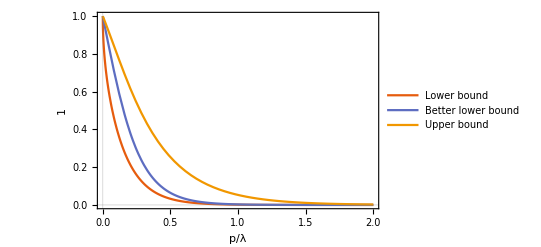

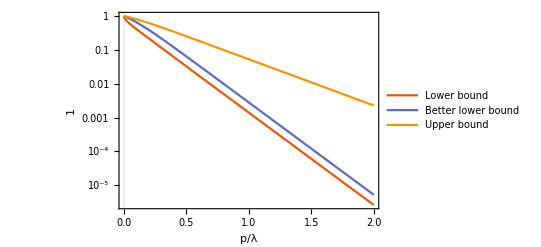

{1-(√(-1+u^2))/((1+u^2+u^4)^(1/4)),(1-u^2+√(1+u^2+u^4))/(√(1+u^2+u^4)),(√(1-u^2+√(1+u^2+u^4)))/((1+u^2+u^4)^(1/4))}

{3/(4 u^2)+3/(32 u^4)+O[1/u]^5,3/(2 u^2)-3/(8 u^4)+O[1/u]^5,(√(3/2))/u-(√(3/2))/(8 u^3)+O[1/u]^5}

```mathematica
{1-√2 (((-1+ⅇ^(Ω/tmp))^2 Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2))^(1/4),1-2 (-1+ⅇ^(Ω/tmp)) √((Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2)),√(1-2 (-1+ⅇ^(Ω/tmp)) √((Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2)))}/.{Ω->p,ωR->p Coth[(π p)/(2λ)],tmp->λ/(2π)};
bounds=Simplify[%,Assumptions->p>0&&λ>0]
Plot[Evaluate[bounds/.λ->1],{p,0,2},PlotTheme->"Scientific",PlotRange->Full,PlotLegends->{"Lower bound", "Better lower bound","Upper bound"},FrameLabel->{"p/λ","1"}]
LogPlot[Evaluate[bounds/.λ->1],{p,0,2},PlotTheme->"Scientific",PlotRange->Full,PlotRange->Full,PlotLegends->{"Lower bound", "Better lower bound","Upper bound"},FrameLabel->{"p/λ","1"}]
FullSimplify[bounds/.p->λ/π Log@u]
Series[%,{u,∞,4}](*u->ⅇ^((π p)/λ)*)
ClearAll[bounds]
```

```mathematica
Sum[(a^m(2m)!)/(m!)^2,{m,0,∞}]
```

1/(√(1-4 a))

{1-(√(-1+ⅇ^((2 p π)/λ)))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4)),(√(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4))}

{1-(√(-1+u))/((1+u+u^2)^(1/4)),(√(1-u+√(1+u+u^2)))/((1+u+u^2)^(1/4))}

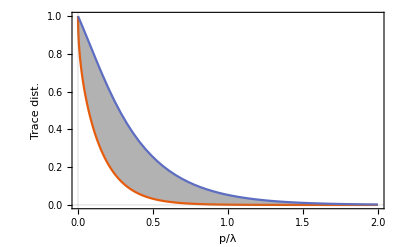

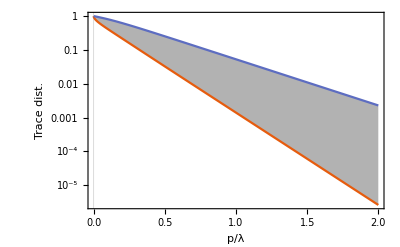

```mathematica
{1-√2 (((-1+ⅇ^(Ω/tmp))^2 Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2))^(1/4),√(1-2 (-1+ⅇ^(Ω/tmp)) √((Ω ωR)/(-(Ω-ωR)^2+ⅇ^((2 Ω)/tmp) (Ω+ωR)^2)))}/.{Ω->p,ωR->p Coth[(π p)/(2λ)],tmp->λ/(2π)};
bounds=Simplify[%,Assumptions->p>0&&λ>0]
ubounds=FullSimplify[bounds/.p->λ/(2π)Log@u]
(*Series[ubounds,{u,∞,2}]
ebounds=Simplify[Normal[%]/.u->ⅇ^((π p)/λ)]*)
Plot[Evaluate[(*Join[*)bounds(*,ebounds]*)/.λ->1],{p,0,2},PlotTheme->"Scientific",PlotRange->Full,Filling->{1->{2}},(*PlotLegends->Placed[{"Lower","Upper"(*"Ext. l.","Ext. u.","App. l.", "App. u."*)},Bottom],*)FrameLabel->{"p/λ","Trace dist."},FrameTicks->Automatic]
(*Export["fidel-nrm.pdf",%]*)
LogPlot[Evaluate[(*Join[*)bounds(*,ebounds]*)/.λ->1],{p,0,2},PlotTheme->"Scientific",PlotRange->Full,PlotRange->Full,Filling->{1->{2}},(*PlotLegends->Placed[{"Lower","Upper"(*"Ext. l.","Ext. u.","App. l.", "App. u."*)},Bottom],*)FrameLabel->{"p/λ","Trace dist."},FrameTicks->Automatic]
(*Export["fidel-log.pdf",%]*)
ClearAll[bounds,ubounds,ebounds]
```

```mathematica
{q,1-(√(-1+u))/((1+u+u^2)^(1/4)),(√(1-u+√(1+u+u^2)))/((1+u+u^2)^(1/4))}/.u->ⅇ^q
(*Plot[%,{q,0,15}]
LogPlot[Evaluate@%%,{q,0,15}]*)
Table[%/.q->n/100.,{n,0,500}];
Export["mesh_trace_dist_mode_bounds.dat",%]
```

{q,1-(√(-1+ⅇ^q))/((1+ⅇ^q+ⅇ^(2 q))^(1/4)),(√(1-ⅇ^q+√(1+ⅇ^q+ⅇ^(2 q))))/((1+ⅇ^q+ⅇ^(2 q))^(1/4))}

mesh_trace_dist_mode_bounds.dat

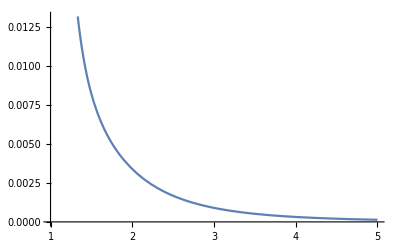

81-351 u^2+513 u^4-336 u^6+96 u^8

3

```mathematica
(*Relaxing bounds*)
Plot[1-(√(-1+u^2))/((1+u^2+u^4)^(1/4))-3/(4 u^2),{u,1,5}]
(1+u^2+u^4)(4 u^2-3)^4-(4 u^2 √(-1+u^2))^4//FullSimplify
%-96(u^2-1)^4-48(u^2-1)^3-81(u^2-1)^2-51(u^2-1)//FullSimplify
```

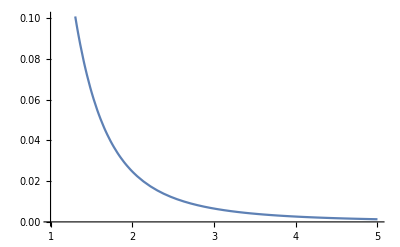

3 (-3+u^2+u^4)

9/4

```mathematica
Plot[(√(3/2))/u-(√(1-u^2+√(1+u^2+u^4)))/((1+u^2+u^4)^(1/4)),{u,1,5}]
FullSimplify[(2 u^2)^2(u^2-1)^2-(u^4+u^2+1)(2 u^2-3)^2]
%-3(u^2-3/2)^2-12(u^2-3/2)//FullSimplify
```

```mathematica
Integrate[1/u Log[(√(-1+u))/((1+u+u^2)^(1/4))],{u,1,∞}]
```

-π^2/9

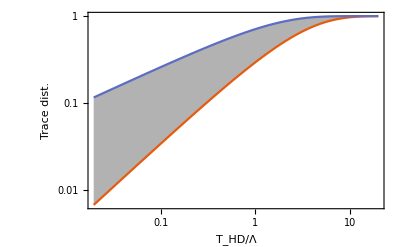

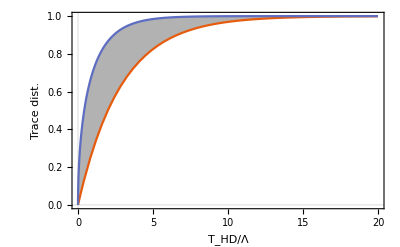

mesh_trace_dist_total_bounds.dat

```mathematica
LogLogPlot[Evaluate[{1-f,√(1-f^2)}/.f->ⅇ^(-(π x)/9)],{x,0,20},PlotTheme->"Scientific",Filling->{1->{2}},FrameLabel->{"T_HD/Λ","Trace dist."},Frame->True,FrameTicks->Automatic]
Plot[Evaluate[{1-f,√(1-f^2)}/.f->ⅇ^(-(π x)/9)],{x,0,20},PlotRange->Full,PlotTheme->"Scientific",Filling->{1->{2}},FrameLabel->{"T_HD/Λ","Trace dist."},Frame->True,FrameTicks->Automatic]
N[Table[{n/40,1-f,√(1-f^2)}/.f->ⅇ^(-π/9 n/40),{n,1,800,2}]];
Export["mesh_trace_dist_total_bounds.dat",%]
(*Export["all-trace.pdf",%]*)
```

```mathematica
{1-(√(-1+ⅇ^((2 p π)/λ)))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4)),(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ)))/(√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))),(√(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4))};
Simplify[Log@%,Assumptions->p>0&&λ>0]
Integrate[%[[1]],{p,0,∞}]
```

{Log[1-(√(-1+ⅇ^((2 p π)/λ)))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4))],Log[(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ)))/(√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ)))],Log[(√(1-ⅇ^((2 p π)/λ)+√(1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4))]}

∫_0^∞ Log[1-(√(-1+ⅇ^((2 p π)/λ)))/((1+ⅇ^((2 p π)/λ)+ⅇ^((4 p π)/λ))^(1/4))]ⅆp

```mathematica
Sum[(ⅇ^(-2β(m1))(2m1)!a1^m1)/(4^m1(m1!)^2),{m1,0,∞}]
Sum[(ⅇ^(-2β(m1))(2m1)!a1^m1)/(4^m1(m1!)^2)(ⅇ^(-2β(m2))(2m2)!a2^m2)/(4^m2(m2!)^2),{m1,0,∞},{m2,0,∞}]
```

1/(√(1-a1 ⅇ^(-2 β)))

1/(√(1-a1 ⅇ^(-2 β)) √(1-a2 ⅇ^(-2 β)))

```mathematica
gfun=Exp[-1/2(d1 x1^2+d2 x2^2+2od x1 x2)];
Integrate[gfun,{x1,-∞,∞},{x2,-∞,∞}];
nfac=FullSimplify[%,Assumptions->Re[od^2/d2]<Re[d1]&&d2>0]^-1
Integrate[nfac gfun,{x1,-∞,∞},{x2,-∞,∞},Assumptions->Re[od^2/d2]<Re[d1]&&d2>0]
Integrate[nfac x1 x2 gfun,{x1,-∞,∞},{x2,-∞,∞},Assumptions->Re[od^2/d2]<Re[d1]&&d2>0]
ClearAll[gfun,nfac]
```

(√(d1 d2-od^2))/(2 π)

1

od/(-d1 d2+od^2)

```mathematica
gfun=Exp[-1/2(d1 x1^2+d2 x2^2)];
Integrate[gfun,{x1,-∞,∞},{x2,-∞,∞}];
nfac=FullSimplify[%,Assumptions->d1>0]^-1
Integrate[nfac gfun,{x1,-∞,∞},{x2,-∞,∞},Assumptions->d1>0]
Integrate[nfac x1 x1 gfun,{x1,-∞,∞},{x2,-∞,∞},Assumptions->d1>0&&d2>0]
ClearAll[gfun,nfac]
```

(√(d1 d2))/(2 π)

1

1/d1

(√(2/π))/(1+v^2)

-(2 √(2/π) (-1+3 v^2))/((1+v^2)^3)

-(4 √(2/π) (-4+3 u^2))/((4+u^2)^3)

-(4 √(2/π) (-4+3 u^2))/((4+u^2)^3)

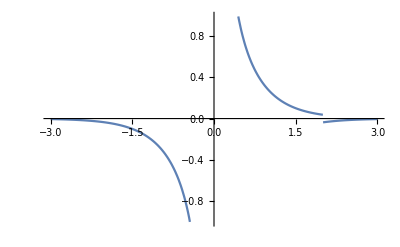

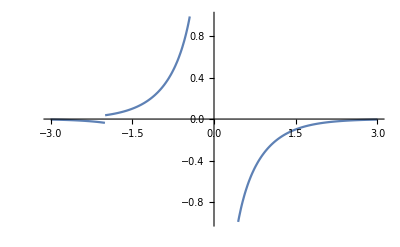

```mathematica
(*verify convolution theorem*)
f=ⅇ^(-Abs[p]);g=p^2 ⅇ^(-Abs[p]);
InverseFourierTransform[f,p,v]
InverseFourierTransform[g,p,v]
1/(√(2π))Convolve[%%,%,v,u]
InverseFourierTransform[f g,p,u]
ClearAll[f,g]
```

```mathematica
f1=InverseFourierTransform[Tanh[(π p)/(2λ)],p,vtmp]
f2=InverseFourierTransform[1/(√(2π)p),p,vtmp]
toCon=FullSimplify[1/(√(2π))f1(f2/.vtmp->vD-vtmp)]
(*1/(√(2π))Convolve[f1,f2,vtmp,v,PrincipalValue->True]*)
Plot[Csch[2v]Sign[2-v],{v,-3,3}]
Plot[Csch[2v]Sign[-2-v],{v,-3,3}]
FullSimplify[Integrate[toCon,{vtmp,vD,+∞},Assumptions->λ>0&&vD>0,PrincipalValue->True],Assumptions->λ>0&&vD>0]
FullSimplify[Integrate[toCon,{vtmp,-vD,vD},Assumptions->λ>0&&vD>0,PrincipalValue->True],Assumptions->λ>0&&vD>0]
FullSimplify[2%%+%]
FullSimplify[Integrate[toCon,{vtmp,vD,+∞},Assumptions->λ>0&&vD<0,PrincipalValue->True],Assumptions->λ>0&&vD<0]
FullSimplify[Integrate[toCon,{vtmp,-vD,vD},Assumptions->λ>0&&vD<0,PrincipalValue->True],Assumptions->λ>0&&vD<0]
FullSimplify[2%%+%]
(*FullSimplify[Integrate[toCon,{vtmp,-vD,vD},Assumptions->λ>0&&vD>0,PrincipalValue->True],Assumptions->λ>0&&vD>0]
FullSimplify[Integrate[toCon,{vtmp,vD,+∞},Assumptions->λ>0,PrincipalValue->True],Assumptions->λ>0]*)
ClearAll[f1,f2,toCon]
(*1/(√(2π))Convolve[%%,%,v,v1-v2]*)
```

-ⅈ √(2/π) λ Csch[vtmp λ]

-1/2 ⅈ Sign[vtmp]

-(λ Csch[vtmp λ] Sign[vD-vtmp])/(2 π)

-Graphics-

-Graphics-

Log[Coth[(vD λ)/2]]/(2 π)

0

Log[Coth[(vD λ)/2]]/π

Log[-Coth[(vD λ)/2]]/(2 π)

0

Log[-Coth[(vD λ)/2]]/π

Log[Coth[vD/2]]/π

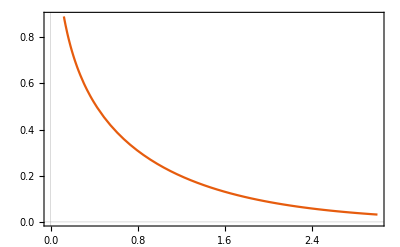

```mathematica
fun=(Log@Coth[vD/2])/π
Plot[fun,{vD,0,3},PlotTheme->"Scientific"]
ClearAll[fun]
```

```mathematica
weight[n_]:=ⅇ^(-(n+1/2)Ω/tmp)
zstand=FullSimplify[∑_(n=0)^(+∞) ⅇ^(-(n+1/2)Ω/tmp)]
FullSimplify[1/(2Ω)1/zstand∑_(n=0)^(+∞) (2n+1)weight[n]]
2%/.{tmp->λ/(2π),Ω->p}
ClearAll[weight,zstand]
```

1/2 Csch[Ω/(2 tmp)]

Coth[Ω/(2 tmp)]/(2 Ω)

Coth[(p π)/λ]/p

```mathematica
1/p ⅇ^(-ⅈ p v);
ComplexExpand[{Re[%],Im[%]}]//FullSimplify
Integrate[%,{p,-∞,∞},PrincipalValue->True]
```

{Cos[p v]/p,-Sin[p v]/p}

Integrate::idiv: Integral of Cos[p v]/p does not converge on {-∞,∞}.

{Integrate[Cos[p v]/p,{p,-∞,∞},PrincipalValue→True],-(π v)/(√(v^2))}

```mathematica
InverseFourierTransform[1/(√(2π)p)Coth[(π p)/λ],p,v]
```

InverseFourierTransform[Coth[(p π)/λ]/(p √(2 π)),p,v]

-(ⅈ λ Coth[(vtmp λ)/2])/(√(2 π))

-1/2 ⅈ Sign[vtmp]

-(λ Coth[(vtmp λ)/2] Sign[vD-vtmp])/(4 π)

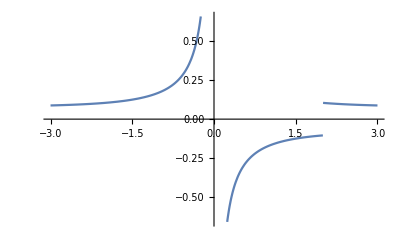

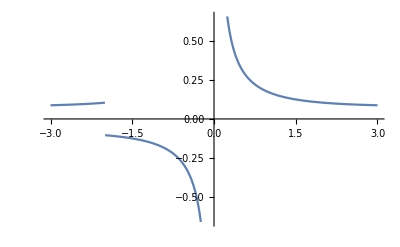

```mathematica
f1=InverseFourierTransform[Coth[(π p)/λ],p,vtmp]
f2=InverseFourierTransform[1/(√(2π)p),p,vtmp]
toCon=FullSimplify[1/(√(2π))f1(f2/.vtmp->vD-vtmp)]
(*1/(√(2π))Convolve[f1,f2,vtmp,v,PrincipalValue->True]*)
Plot[Evaluate[toCon/.{λ->1,vD->2}],{vtmp,-3,3}]
Plot[Evaluate[toCon/.{λ->1,vD->-2}],{vtmp,-3,3}]
(*toInt=FullSimplify[toCon ⅇ^(-ϵ vtmp),Assumptions->λ>0&&vtmp>vD&&vD>0&&ϵ>0]
FullSimplify[Integrate[toInt,{vtmp,vD,+∞},Assumptions->λ>0&&vD>0&&ϵ>0,PrincipalValue->True],Assumptions->λ>0&&vD>0]
Limit[%,ϵ->0,Direction->-1]*)
(*FullSimplify[Integrate[toCon,{vtmp,-vD,vD},Assumptions->λ>0&&vD>0,PrincipalValue->True],Assumptions->λ>0&&vD>0]
FullSimplify[2%%+%]
FullSimplify[Integrate[toCon,{vtmp,vD,+∞},Assumptions->λ>0&&vD<0,PrincipalValue->True],Assumptions->λ>0&&vD<0]
FullSimplify[Integrate[toCon,{vtmp,-vD,vD},Assumptions->λ>0&&vD<0,PrincipalValue->True],Assumptions->λ>0&&vD<0]
FullSimplify[2%%+%]*)
(*FullSimplify[Integrate[toCon,{vtmp,-vD,vD},Assumptions->λ>0&&vD>0,PrincipalValue->True],Assumptions->λ>0&&vD>0]
FullSimplify[Integrate[toCon,{vtmp,vD,+∞},Assumptions->λ>0,PrincipalValue->True],Assumptions->λ>0]*)
ClearAll[f1,f2,toCon,toInt]
```

```mathematica
InverseFourierTransform[1/p,p,x]
```

-ⅈ √(π/2) Sign[x]

```mathematica
Table[{q,1/(2q),1/(2q)Tanh[q/4],Coth[q/2]/(2q)}/.q-> 1. 10^(n/10),{n,-14,15}];
Export["mesh_fluc_fourier.dat",%]
```

mesh_fluc_fourier.dat

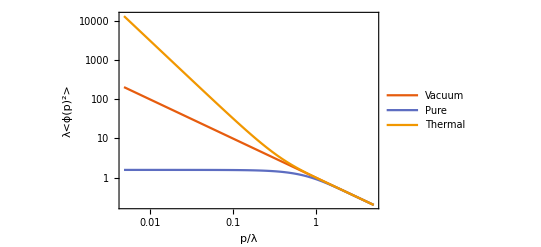

psd.pdf

```mathematica
fig=LogLogPlot[Evaluate[{1/p,1/p Tanh[(π p)/(2λ)],Coth[(p π)/λ]/p}/.λ->1],{p,0,5},PlotLegends->Placed[{"Vacuum","Pure","Thermal"},Below],FrameLabel->{"p/λ","λ<ϕ(p)^2>"},PlotTheme->"Scientific",Frame->True,FrameTicks->Automatic]
Export["psd.pdf",fig]
ClearAll[fig]
```